```mathematica
roots = NSolve[∫_0^π Abs[Tanh[β*Sqrt[1+0.1^2-2*0.1 *Cos[t]]]]^2 ⅆt== 0 && -10<Re[β]<10 && -10<Im[β]<10, β ]
```

```mathematica
NSolve[∫_0^π Abs[Tanh[β √(1.01-0.2 Cos[t])]]^2 ⅆt==0&&-10<Re[β]<10&&-10<Im[β]<10,β]
```

NSolve[∫_0^π Abs[Tanh[β √(1.01-0.2 Cos[t])]]^2 ⅆt==0&&-10<Re[β]<10&&-10<Im[β]<10,β]

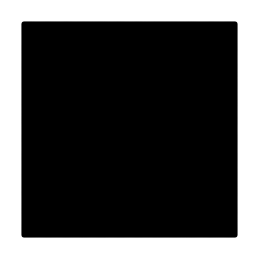

```mathematica
list=Flatten[Table[{{β},∫_0^π Abs[Tanh[β*Sqrt[1+0.1^2-2*0.1 *Cos[t]]]]^2 ⅆt},{β,-10,10,1/10}]];
Graphics@Point@list
```

```mathematica
MeshCoordinates
```

```mathematica
∫_0^π Abs[Tanh[10*Sqrt[1+0.5^2-2*0.5 *Cos[t]]]]^2 ⅆt
```

$Aborted

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1137464+ⅈ π Charting`Private`pvar$1137465) √(1.49+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141593}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

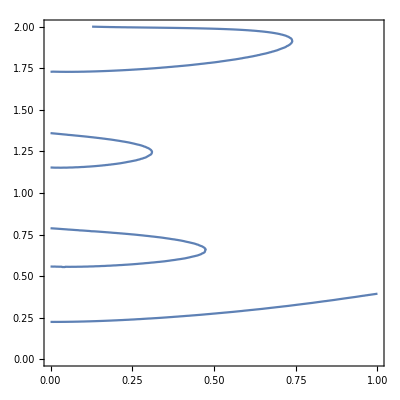

```mathematica
Clear[g,q]
ϵ =√(1+g^2-2 g*Cos[q]); g=0.7;
Z[x_,y_] := NIntegrate[Log[Abs[Tanh[(x+y I)*ϵ]]^2],{q,0,π},WorkingPrecision->7]
ContourPlot[Z[x,y*π]==0,{x,0,1},{y,0,2}]
```

NIntegrate::inumr: The integrand Log[Tanh[(Charting`Private`pvar$888139-ⅈ π Charting`Private`pvar$888140) √(1.49-1.4 Cos[«1»])] Tanh[(Charting`Private`pvar$888139+ⅈ π Charting`Private`pvar$888140) √(1.49-1.4 Cos[«1»])]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

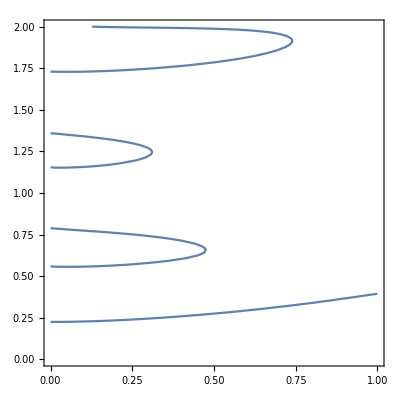

```mathematica
Clear[g,q]
ϵ =√(1+g^2-2 g*Cos[q]); g=0.7;
Z[x_,y_] := NIntegrate[Log[Tanh[(x+y I)*ϵ]*Tanh[(x-y I)*ϵ]],{q,0,π},WorkingPrecision->10]
ContourPlot[Re[Z[x,y*π]]==0,{x,0,1},{y,0,2}]
```

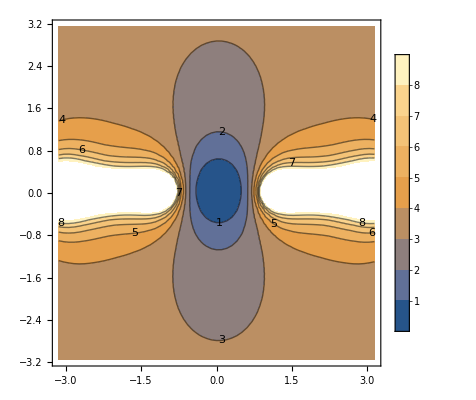

```mathematica
ListContourPlot[Table[int[x,y],{x,-π,π,0.1},{y,-π,π,0.1}],DataRange->{{-π,π},{-π,π}},PlotLegends->Automatic,ContourLabels->All]
```

```mathematica
ListPlot3D[Table[int[x,y],{x,-π,π,0.1},{y,-π,π,0.1}]]
```

```mathematica
Manipulate[ListContourPlot[Table[NIntegrate[Abs[Tanh[(x+y I)*Sqrt[1+g^2-2*g *Cos[t]]]]^2,{t,0,π}],{x,-π,π,0.1},{y,-π,π,0.1}],Contours->0,DataRange->{{-π,π},{-π,π}},PlotLegends->Automatic,ContourLabels->All],{g,0,1,0.1}]
```

```mathematica
Clear[g,q]
Manipulate[ContourPlot[NIntegrate[Log[Abs[Tanh[(x+y *π I)*Sqrt[1+g^2-2 g*Cos[q]]]]^2],{q,0,π},WorkingPrecision->10]==0,{x,0,1},{y,0,2}],{g,0,1,0.1}]
```

NIntegrate::inumr: The integrand Log[Abs[Tanh[Charting`Private`pvar$1409880+ⅈ π Charting`Private`pvar$1409881]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1488317+ⅈ π Charting`Private`pvar$1488318) √(1.01+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1608552+ⅈ π Charting`Private`pvar$1608553) √(1.04+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

NIntegrate::inumr: The integrand Log[Abs[Tanh[1. (Charting`Private`pvar$1608552+ⅈ π Charting`Private`pvar$1608553)]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[1. (Charting`Private`pvar$1616549+ⅈ π Charting`Private`pvar$1616550)]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1688808+ⅈ π Charting`Private`pvar$1688809) √(1.01+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1688808+ⅈ π Charting`Private`pvar$1688809) √(2.+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1809091+ⅈ π Charting`Private`pvar$1809092) √(1.49+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1809091+ⅈ π Charting`Private`pvar$1809092) √(1.81+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1817080+ⅈ π Charting`Private`pvar$1817081) √(1.81+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1817080+ⅈ π Charting`Private`pvar$1817081) √(1.36+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$1984548+ⅈ π Charting`Private`pvar$1984549) √(1.36+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$2126844+ⅈ π Charting`Private`pvar$2126845) √(1.36+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$2277097+ⅈ π Charting`Private`pvar$2277098) √(1.49+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$2742504+ⅈ π Charting`Private`pvar$2742505) √(1.81+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

NIntegrate::inumr: The integrand Log[Abs[Tanh[(Charting`Private`pvar$2742504+ⅈ π Charting`Private`pvar$2742505) √(1.04+Times[«2»])]]^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.141592654}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
Manipulate[ContourPlot[a x^2+y^2==1,{x,-2,2},{y,-2,2}],{a,0,2,0.1}]
```

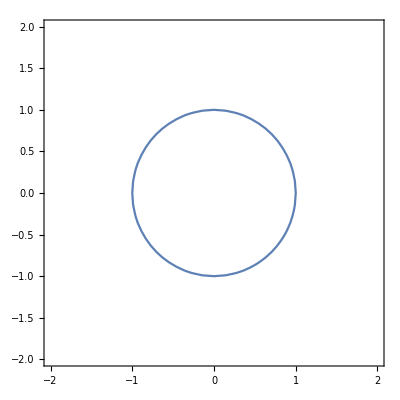

```mathematica
ContourPlot[x^2+y^2==1,{x,-2,2},{y,-2,2}]
Manipulate[ContourPlot[a x^2+y^2==1,{x,-2,2},{y,-2,2}],{a,0,1,0.01}]
```